# Jessica Weed - Take Home Portion Final Exam

## 1.

Using the definition of the Laplace Transform, find the Laplace Transform of the following function
	
		f(t) = 	2	0 < t < 3
			e^t	t ≧ 3
		
Definition of Laplace Transform:
Let f be a function defined for t ≧ 0. Then the integral

	ℒ { f(t) } = ∫∞
0 e^-stf (t) dt
is said to be the Laplace Transform of f, provided that the integral converges.

ℒ { f(t) } = ∫3
0 e^-st(2) dt + ∫∞
3 e^-st (e^t) dt

ℒ { f(t) } = ∫3
0 e^-st(2) dt + ∫∞
3 e^(t-st) dt

ℒ { f(t) } = -(2 e^-st)/s|3
0 + ∫∞
3 e^(t-st) dt

ℒ { f(t) } = -(2 e^-st)/s|3
0 + lim_(b → ∞) ∫b
3 e^(-t(s-1)) dt

ℒ { f(t) } = -(2 e^-st)/s|3
0 + lim_(b → ∞)  -e^(-t (s-1))/(s-1)|b
3
ℒ { f(t) } = -(2 e^(-(3)s))/s+(2 e^(-(0)s))/s+ lim_(b → ∞) [ -e^(-b (s-1))/(s-1)+ e^(0(s-1))/(s-1)]
ℒ { f(t) } = -(2 e^(-(3)s))/s+(2(1))/s+ lim_(b → ∞) [ e^(-b (s-1))/(s-1)+ 1/(s-1)]
As b approaches ∞ the term e^(-b (s-1))/(s-1) goes to 0 because e^(-∞ (s-1)) approaches 0 (as long as s > 1). The term 1/(s-1)is not dependent on b so it will not be affected when b approaches ∞, so it is significant in this case.
Therefore: 
ℒ { f(t) } =  -(2 e^(-3s))/s+2/s+ 1/(s-1), s > 1

## 2.

Consider the following ordinary differential equation: 

		dy/dx= x/y
		
	a. Use DSolve[] in Mathematica to find the general form of the solution y(x).

```mathematica
DSolve[{y'[x]==x/y[x]},y[x],x]
```

{{y[x]→-√(x^2+2 C[1])},{y[x]→√(x^2+2 C[1])}}

b. Explain, using concepts or theorems from class, why you see the output that you do. In other words, WHY you see two answers. 
This o.d.e. has multiple solutions.  They both have the same interval of existence but lie mirrored over the xy plane in comparison to one another.  At -2 C_1≥ x the solutions are no longer defined, however the o.d.e. is defined. When taking the square root of both sides, you take away half of the interval that the ode is defined.  So the - and + functions in this case cover the entire interval during which the o.d.e. is defined.

This would work for any constant, C1, but as an example, I set C1 to 2.

```mathematica
C1 = 50
```

50

```mathematica
a = -√(x^2+2 C1)
```

-√(100+x^2)

```mathematica
b = √(x^2+2 C1)
```

√(100+x^2)

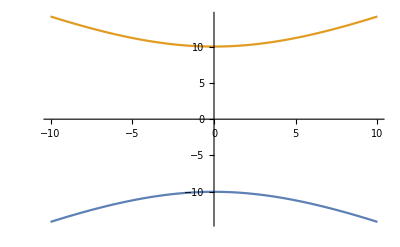

```mathematica
Plot[{a,b},{x,-10,10}]
```

c. Solve the O.D.E. by hand using separation of variables.
	
	dy/dx=x/y
	y dy = x dx
	∫ y dy = ∫ x dx
	1/2 y^2= 1/2 x^2+ c_1
	y^2= x^2 + 2 c_1
	y = ±√ x^2+ 2 c_1

## 3.

Consider the following ordinary differential equation
		
		x^2y’’ + 4xy’ + 2y = g(x)
		
where g(x) is a nonzero, differentiable function. This o.d.e. has the following particular solution

		y_p= (-1 + 6/x^2) cos(x) + (4sin(x))/x
Find, by hand, the general solution to the nonhomogeneous o.d.e.

Answer:

The homogeneous equation is: 

x^2y'' + 4xy' + 2y = 0

a = 1
b = 4
c = 2

Assume the solution takes the form y = x^m

y = x^m		y' = mx^(m-1) 	 y''= (m-1)m x^(m-2)

x^2(m-1) mx^(m-2)+ 4 xmx^(m-1)+ 2 x^m = 0
(m-1) m x^m+ 4 mx^m + 2 x^m= 0
x^m[(m-1)m + 4m + 2] = 0	We know x^mwill not be zero at any time as long as x is not zero, so I can disregard it being a root.
(m-1)m + 4m + 2 = 0
m^2- m + 4m + 2 = 0 
m^2+ 3m + 2 = 0

```mathematica
Roots[m^2+ 3m + 2 ==0, m]
```

m==-2||m==-1

Therefore, the roots of the auxiliary equation are m = -2 and m = -1.
For the homogeneous equation, the solution is:

y_c = c_1 x^-1+ c_2 x^-2

However, we must include the particular solution.

y = y_c+ y_p
y = c_1 x^-1+ c_2 x^-2+ (-1 + 6/x^2) cos(x) + (4sin(x))/x

## 4.

(For my case - because Mathematica keeps autocorrecting my subscripts- I will be using x for rabbit population and y for hunter population)
Let a population of rabbits and hunters be descibed by

	dx/dt= 10x - 100xy
	dy/dt= 10xy - 7y
	
Where x(t) represents the rabbit population and y(t) represents the hunter population in the Looney Toons forest in a particular year, t after the year 2015. (Note, this means that t=0 is the moment the year 2016 begins and t=1 is the very end of 2016 or beginning of 2017). x(t) and y(t) are positive. 

a. Some characters in the Looney Toons forest are not happy with the number of rabbits, which at the very end of 2015 will be 5 rabbits.  Hence, at t=0, rabbit season will begin.  If Elmer Fudd and his wife are the only hunters (at t=0), write an initial value problem for which the solution desribes the number of rabbits in the Looney Toons forest at time t and the number of hunters in the forest at time t. 

Solve dx/dt= 10x - 100xy 
	subject to x(0) = 5.
This will give us the number of rabbits in the forest at time t.

Solve dy/dt= 10xy - 7y
	subject to y(0) = 2
This will give us the number of hunters in the forest at time t.

b. Use NDSolve in Mathematica to find numerical solutions for the IVP you found in 4a.  Plot these solutions in Mathematica. Label your plots well. (Do not create plots for more than a few years in the future for this part of the problem.)

{{x[t]→InterpolatingFunction[{{0., 5.}}, <>][t],y[t]→InterpolatingFunction[{{0., 5.}}, <>][t]}}

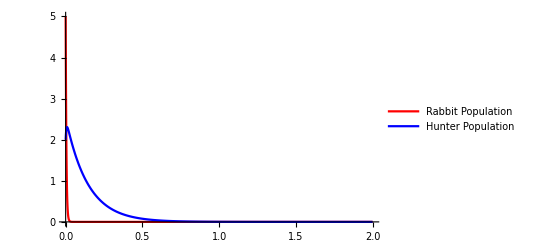

```mathematica
soln = NDSolve[{x'[t]==10x[t]-100x[t]*y[t],y'[t]==10x[t] y[t]-7y[t],x[0]==5,y[0]==2},{x[t],y[t]},{t,0,5}]
Plot[{x[t]/.soln,y[t]/.soln},{t,0,2},PlotStyle->{Red,Blue}, PlotLegends->{"Rabbit Population","Hunter Population"},PlotRange->All]
```

c. Will Bugs Bunny and his friends all be killed by the hunters? 
	Yes. According to the graph above, they will be killed very quickly by the hunters.

{{x[t]→InterpolatingFunction[{{0., 10.}}, <>][t],y[t]→InterpolatingFunction[{{0., 10.}}, <>][t]}}

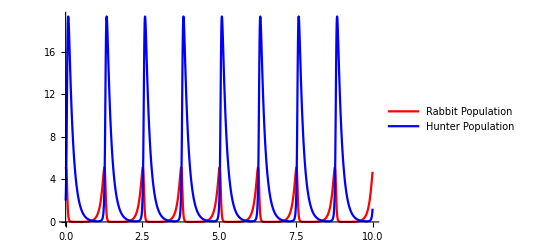

```mathematica
soln = NDSolve[{x'[t]==10x[t]-3x[t]*y[t],y'[t]==10x[t] y[t]-7y[t],x[0]==5,y[0]==2},{x[t],y[t]},{t,0,10}]
Plot[{x[t]/.soln,y[t]/.soln},{t,0,10},PlotStyle->{Red,Blue}, PlotLegends->{"Rabbit Population","Hunter Population"},PlotRange->All]
```

I chose to change the death rate of the rabbits based on the encounter rate of the rabbits and hunters from 100 to 3.  The rabbits were dying out too quickly and in turn the hunters were also dying because their population relies on hunting the rabbits.  Above in the graph, you can see the cyclic rate of the rabbits’ and hunters’ populations without any kind of damping - the amplitude of both populations remain constant at their peaks.  I decreased the death rate of rabbits based on the encounter rate because the rabbits are able to run away and in the model given, it was definite that they would not be able to do so.